```mathematica
(Integrate[7.55*x,{x,1671.7,1709.1}] + Integrate[5.5*x,{x,1709.1,1725.1}] + Integrate[3.2*x,{x,1725.1,1736.1}] +Integrate[x,{x,1736.1,1737.1}]) /Integrate[x,{x,1671.7,1737.1}]
```

6.19979

```mathematica
data ={ {1697.1,7.55},{1709.1,5.5},{1725.1,3.2},{1736.1,1}};
```

```mathematica
NonlinearModelFit[data,a^2-b^2 x^2,{a,b},x]
```

FittedModel[145.46-0.0000478823 x^2]

```mathematica
nlm=NonlinearModelFit[data, a^2 -b^2 x^2,{a,b},x]
```

FittedModel[145.46-0.0000478823 x^2]

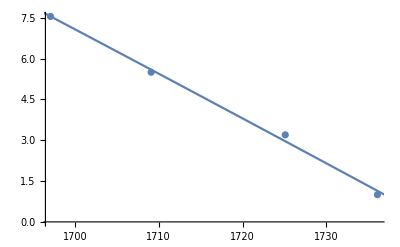

```mathematica
Show[ListPlot[data],Plot[nlm[x],{x,1677.1,1737.1}]]
```

```mathematica
145.45981755598535-0.00004788232031284735 (1671.7)^2
```

11.6488